```mathematica
d=4
G[w_,L_,t_]:=Sum[
Exp[-(Pi * k * w /(2*L))^2]*
Exp[-d*(Pi*k/L)^2*t],
{k,-Infinity,Infinity}] /
Sum[
Exp[-(Pi * k * w /(2*L))^2],
{k,-Infinity,Infinity}]
```

4

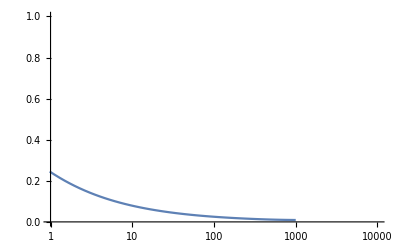

```mathematica
LogLinearPlot[G[1,100,t],{t,0,1000},
PlotRange->{{1,10000}, {0,1}}]
```

### Get an expression for a finite Fourier transform of the incoherent intermediate scattering function. FF are the fourier series elements

```mathematica
ClearAll[d]
F[r_,t_]:=1/(2*Sqrt[d*t*Pi])*Exp[-r^2/(4*d*t)]
Integrate[Exp[-I*k*r]*F[r,t],{r,-Infinity,Infinity},Assumptions-> {Re[1/(d*t)]>0,L∈Reals,L>0,d∈Reals,d>0,t∈Reals}]//FullSimplify

FF[k_,t_]:= 1/L * Integrate[Exp[-I*k*r]*F[r,t],{r,-L,L},Assumptions-> {Re[1/(d*t)]>0,L∈ Reals,L>0}]//FullSimplify
FF[k,t]
```

ⅇ^(-d k^2 t)

(√d ⅇ^(-d k^2 t) √t (Erf[(L-2 ⅈ d k t)/(2 √d √t)]+Erf[(L+2 ⅈ d k t)/(2 √d √t)]))/(2 L √(d t))

### Do the same for the beam profile W(r) to get the Fourier series element W_K

```mathematica
W[r_]:=1/(w*Sqrt[Pi])Exp[-r^2/w^2]

(* Sanity check to make sure this returns the expected W(q)*)
Integrate[Exp[-I*k*r]*W[r],{r,-Infinity,Infinity},Assumptions->{w∈Reals,w>0,L∈Reals,L>0}]

FW[k_]:=1/L*Integrate[Exp[-I*k*r]*W[r],{r,-L,L},Assumptions->{w∈Reals,w>0,L∈Reals,L>0}]
FW[k]
```

ⅇ^(-1/4 k^2 w^2)

(ⅇ^(-1/4 k^2 w^2) (Erf[L/w-(ⅈ k w)/2]+Erf[L/w+(ⅈ k w)/2]))/(2 L)

### Now combine them, to get the spatially-limited autocorrelation G(t;w;L)

```mathematica
ClearAll[L,w,t,k]
```

```mathematica
BOUND=1;
G[t_,W_,l_]:=
Sum[Abs[FW[k]]^2 * FF[k,t],{k,-BOUND,BOUND}]/
Sum[Abs[FW[k]]^2 * FF[k,tp],{k,-BOUND,BOUND}]/.{L->l,w->W}
```

```mathematica
Gc=Compile[{t,w,l},Sum[Abs[FW[k]]^2 * FF[k,t],{k,-BOUND,BOUND}]/
Sum[Abs[FW[k]]^2 * FF[k,tp],{k,-BOUND,BOUND}]/.{L->l,w->W}]
```

CompiledFunction[…]

```mathematica
G[t,w,L]
```

((Erf[200]^2 Erf[250/(√t)])/1000000000+1/4000000000 ⅇ^(-25/2-4 t) Abs[Erf[200+(5 ⅈ)/2]-ⅈ Erfi[5/2+200 ⅈ]]^2 (Erf[(250-2 ⅈ t)/(√t)]+Erf[(250+2 ⅈ t)/(√t)]))/((Erf[200]^2 Erf[25000000])/1000000000+(Abs[Erf[200+(5 ⅈ)/2]-ⅈ Erfi[5/2+200 ⅈ]]^2 (Erf[25000000+ⅈ/50000]-ⅈ Erfi[1/50000+25000000 ⅈ]))/(4000000000 ⅇ^(31250000001/2500000000)))

```mathematica
Gc[10,10,100]//N
```

1.

```mathematica
G[10000,10,100]/.{L->1,d->1,w->1,tp->.0000000000001}//N
(*Took 143s to evaluate. In the denominator of this, you can see a division by tp, but tp should be zero.*)
```

0.276326+0. ⅈ

```mathematica
d=4;
tp=1*^-10;
Table[Gc[t,10,100],{t,1*^-10,10000,2000}]//N
```

{1.,0.5708,0.423847,0.351921,0.307365}

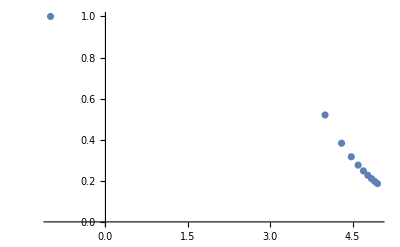

```mathematica
d=1;
tp=1*^-10;
ListPlot[Table[{Log10[t],Gc[t,10,100]},{t,1*^-1,100000,10000}],PlotRange->Full]
```

```mathematica
MemoryInUse[]
```

269198920

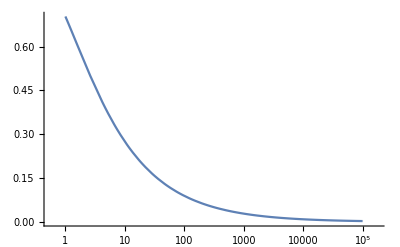

```mathematica
d=1;
L=10;
w=10;
tp=1*^-10;
BOUND=2;
Show[
LogLinearPlot[Gc[t,w,L],{t,1,1*^5},PerformanceGoal->"Speed",GridLines->{{w^2/(4*d)},{0.5}}]]
```

```mathematica
ClearAll[L,w]
w=20;
L=100;
FindRoot[Re[Gc[t,w,L]]-0.5,{t,1+w^2/(4*d)}]
w^2/(4*d)
```

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {101.}. Try perturbing the initial point(s).

{t→101.}

100

```mathematica
Erf[I*Infinity]
```

ⅈ ∞

```mathematica
FF[k,t]//PowerExpand
(*The argument to Erf has an L/(2*Sqrt{d*t}) which is problematic at t=0*)
```

1/(2 (-ⅈ+2 k t))ⅇ^(-k^2 t) ((-ⅈ+2 k t) Erf[(1-2 ⅈ k t)/(2 √t)]-ⅈ √t √(4 ⅈ k+1/t-4 k^2 t) Erf[1/2 √(4 ⅈ k+1/t-4 k^2 t)])